1

1.6

0.99

1.6

1

0.99

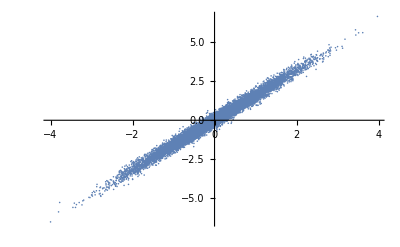

```mathematica
(*First*)
pop1=RandomReal[MultinormalDistribution[{0,0},{{1,0},{0,1}}],10000];
pop1alt=RandomReal[MultinormalDistribution[{1,0},{{1,0},{0,1}}],10000];
pop2=RandomReal[MultinormalDistribution[{0,0},{{1,0.5},{0.5,1}}],10000];
pop3=RandomReal[MultinormalDistribution[{0,0},{{1,-0.5},{-0.5,1}}],10000];
pop4=RandomReal[MultinormalDistribution[{0,0},{{0.2,-0.3},{-0.3,1}}],10000];
x=0;
σ0=1
σ1=1.6
ρ=0.99
pop5=RandomReal[MultinormalDistribution[{0,0},{{σ0^2,ρ*σ0*σ1},{ρ*σ0*σ1,σ1^2}}],10000];
x=0;
σ0=1.6
σ1=1
ρ=0.99
pop6=RandomReal[MultinormalDistribution[{0,0},{{σ0^2,ρ*σ0*σ1},{ρ*σ0*σ1,σ1^2}}],10000];

ListPlot[pop5]
```

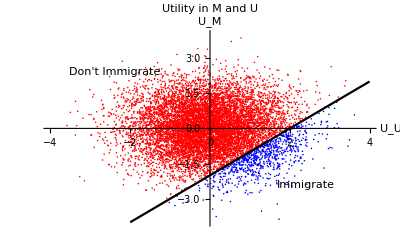

/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_HighCost.pdf

0.200922

0.0479216

```mathematica
x=2;
pop1U=Flatten[Take[pop1,All,1]];
pop1M=Flatten[Take[pop1,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Utility in M and U",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_HighCost.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

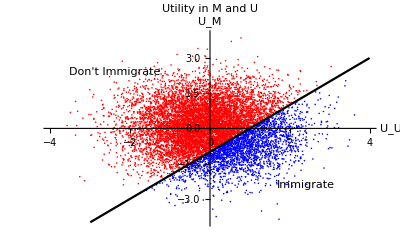

/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_MidCost.pdf

0.428599

0.193699

```mathematica
x=1;
pop1U=Flatten[Take[pop1,All,1]];
pop1M=Flatten[Take[pop1,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Utility in M and U",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_MidCost.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

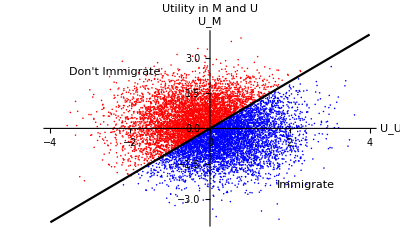

/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_NoCost.pdf

0.554816

0.554816

```mathematica
x=0;
pop1U=Flatten[Take[pop1,All,1]];
pop1M=Flatten[Take[pop1,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Utility in M and U",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_NoCost.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

```mathematica
AvgUtGain
```

0.843476

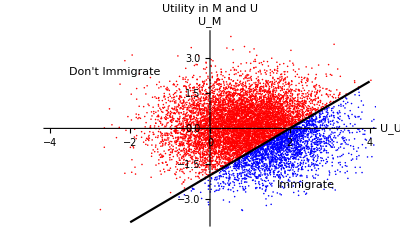

/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_HighCost_Shift.pdf

0.673496

0.198096

```mathematica
x=2;
pop1U=Flatten[Take[pop1alt,All,1]];
pop1M=Flatten[Take[pop1alt,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Utility in M and U",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_HighCost_Shift.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

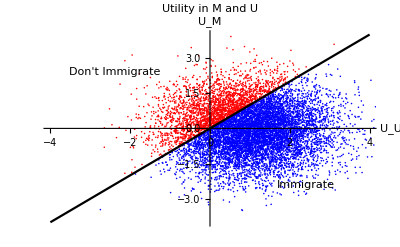

/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_NoCost_Shift.pdf

1.19194

1.19194

```mathematica
x=0;
pop1U=Flatten[Take[pop1alt,All,1]];
pop1M=Flatten[Take[pop1alt,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Utility in M and U",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/Immigration_NoCorr_NoCost_Shift.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

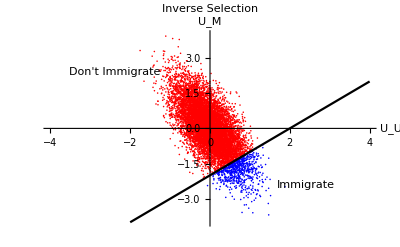

/Users/Tgallen/Dropbox/Yana/InverseSorting.pdf

0.175597

0.0391969

```mathematica
x=2;
pop1U=Flatten[Take[pop4,All,1]];
pop1M=Flatten[Take[pop4,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Inverse Selection",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/InverseSorting.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

1

1.6

0.99

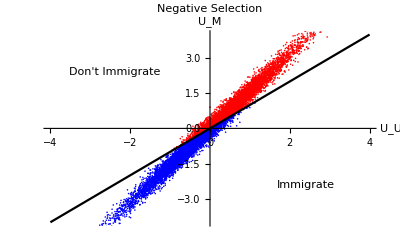

/Users/Tgallen/Dropbox/Yana/NegativeSelection.pdf

0.253989

0.253989

```mathematica
pop1U=Flatten[Take[pop5,All,1]];
pop1M=Flatten[Take[pop5,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Negative Selection",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/NegativeSelection.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

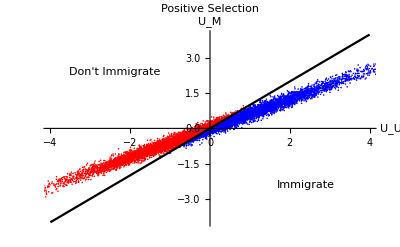

/Users/Tgallen/Dropbox/Yana/PositiveSelection.pdf

0.248915

0.248915

```mathematica
x=0;
pop1U=Flatten[Take[pop6,All,1]];
pop1M=Flatten[Take[pop6,All,{2,2}]];
bestU=MapThread[(Boole[(#1-x>#2)]*#1)+(Boole[(#1-x<=#2)]*#1)&,{pop1U,pop1M}];
Mbest=MapThread[Boole[(#1-x<=#2)]&,{pop1U,pop1M}];
Ubest=1-Mbest;
Mbestind=Position[Mbest,1];
Ubestind=Position[Ubest,1];
xM=Extract[pop1U,Mbestind];
yM=Extract[pop1M,Mbestind];
xU=Extract[pop1U,Ubestind];
yU=Extract[pop1M,Ubestind];
temp=Show[ListPlot[{Partition[Riffle[xM,yM],2],Partition[Riffle[xU,yU],2]},PlotStyle->{Red,Blue},PlotLabel->"Positive Selection",AxesLabel->{"U_U","U_M"},PlotRange->{{-4,4},{-4,4}}],Graphics[Text["Immigrate",{2.4,-2.4}]],Graphics[Text["Don't Immigrate",{-2.4,2.4}]],Plot[z-x,{z,-4,4},PlotStyle->{Black},PlotRange->{{-4,4},{-4,4}}]]
Export["/Users/Tgallen/Dropbox/Yana/PositiveSelection.pdf",temp]
AvgUtGain1=Mean[MapThread[Boole[(#1-x>#2)]*(#1-#2)&,{pop1U,pop1M}]]
AvgUtGain2=Mean[MapThread[Boole[(#1-x>#2)]*(#1-x-#2)&,{pop1U,pop1M}]]
```

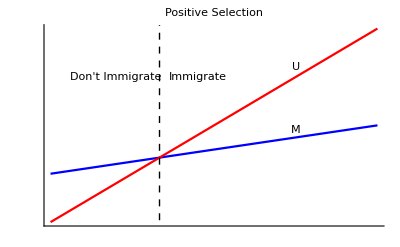

/Users/Tgallen/Dropbox/Yana/PositiveSelectionRoy.pdf

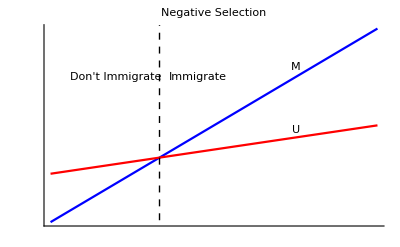

/Users/Tgallen/Dropbox/Yana/NegativeSelectionRoy.pdf

```mathematica
temp=Show[Plot[{1+0.5*s,0.5+2*s},{s,0,1},PlotStyle->{Blue,Red},Ticks->None,PlotLabel->"Positive Selection"],Graphics[Text["U",{0.75,2.1}]],Graphics[Text["M",{0.75,1.45}]],Graphics[Text["Immigrate",{0.45,2}]],Graphics[Text["Don't Immigrate",{0.2,2}]],Graphics[{Dashed,Line[{{1/3,0},{1/3,3}}]}]]
Export["/Users/Tgallen/Dropbox/Yana/PositiveSelectionRoy.pdf",temp]
temp=Show[Plot[{0.5+2*s,1+0.5*s},{s,0,1},PlotStyle->{Blue,Red},Ticks->None,PlotLabel->"Negative Selection"],Graphics[Text["M",{0.75,2.1}]],Graphics[Text["U",{0.75,1.45}]],Graphics[Text["Immigrate",{0.45,2}]],Graphics[Text["Don't Immigrate",{0.2,2}]],Graphics[{Dashed,Line[{{1/3,0},{1/3,3}}]}]]
Export["/Users/Tgallen/Dropbox/Yana/NegativeSelectionRoy.pdf",temp]
```

```mathematica
Solve[1+0.5*s==0.5+2*s]
```

{{s→0.333333}}